```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

```mathematica
evo = Module[
{deep=100,cut=100(*,ru, cas, outputs, fit*)},
SeedRandom[426783];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
cas = Table[CellularAutomaton[ru,Join[Table[1,j],{2}], cut], {j, 5}],
outputs = Length[{{"[◼]", "nonzeroRange"}}[#[[{{"[◼]", "TestCALifeTime"}}[#]/.-Infinity->-1]]]]&/@ cas,
fit = Total[Abs[{4, 6, 8, 10, 12} - outputs]],
If[fit<=Last[#],{ru,fit},#]
]&,{{0, 4, 1},30},deep]
];
```

```mathematica
evo = Module[
{deep=500,cut=100(*,ru, cas, outputs, fit*)},
SeedRandom[426785];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
cas = Table[CellularAutomaton[ru,Join[Table[1,j],{2}], cut], {j, 5}],
outputs = Length[{{"[◼]", "nonzeroRange"}}[#[[-1]]]]&/@ cas,
fit = Total[Abs[{4, 6, 8, 10, 12} - outputs]],
If[fit<=Last[#],{ru,fit},#]
]&,{{0, 4, 1},40},deep]
];
```

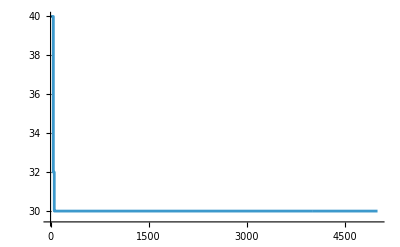

```mathematica
ListStepPlot[evo[[All, -1]], PlotRange->All]
```

```mathematica
evo[[-1]]
```

{{63103342777267004265199288686218836220,4,1},30}

```mathematica
fit
```

30

```mathematica
ResourceFunction["RandomCA"][{4, 1}]
```

<|RuleNumber→32188355144658238937280601882610036557,Colors→4|>

```mathematica
Iconize[evo]
```

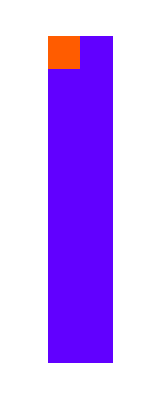
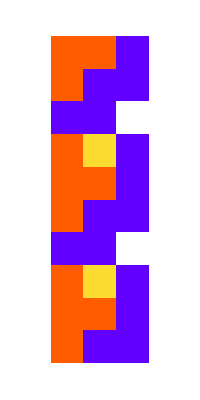
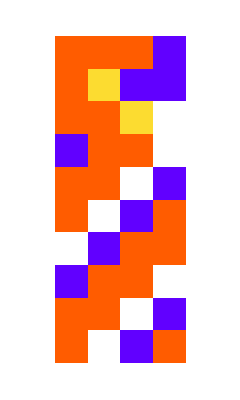
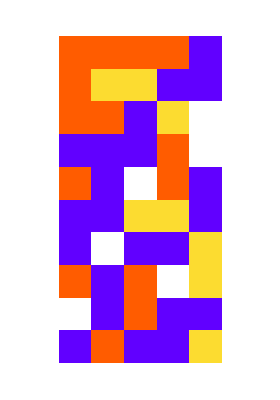
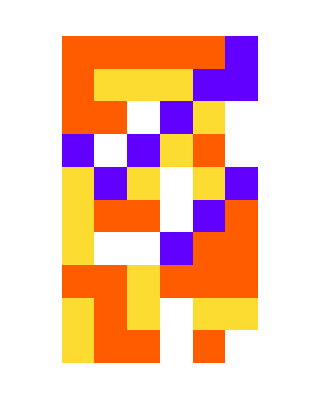

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@#, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@ cas[[All, ;;10]]
```

```mathematica
ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[evo[[-1, 1]], ], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

```mathematica
Iconize[evo]
```

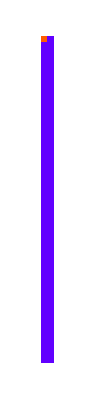
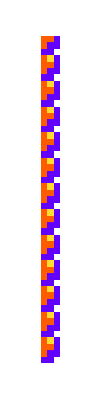
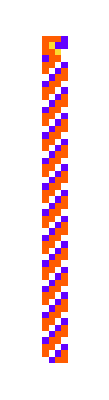
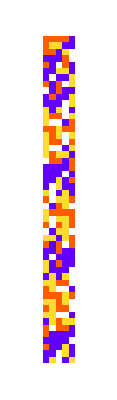
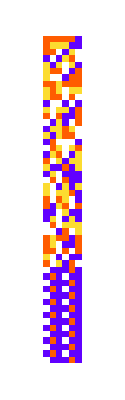

```mathematica
Table[ArrayPlot[ArrayPad[#, 5]&/@CellularAutomaton[evo[[-1, 1]],Join[Table[1,j],{2}], 50],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], {j, 5}]
```